```mathematica
SetDirectory["/Users/danikaluntz-martin/Desktop/Advanced Lab/DoubleSlit-ED"];
countsnear2 = Import["20141122_single_slit_near2.csv"];
countsnear2;
ListPlot[countsnear2, AxesLabel->{Distance (mm),Counts}];
```

```mathematica
θ = (x - x0)/R;
α = π * a * Sin[θ]/λ;
β = π * d * Sin[θ]/λ; 

Subscript[i, 2] = i0/4 * (Sinc[α])^2 ;

x0= 6.6;
a = 0.085;
d = 0.343;
R = 500;
λ = .000546;
```

```mathematica
fitnear2 = NonlinearModelFit[countsnear2,Subscript[i, 2],{i0}, x];
Normal[fitnear2];
```

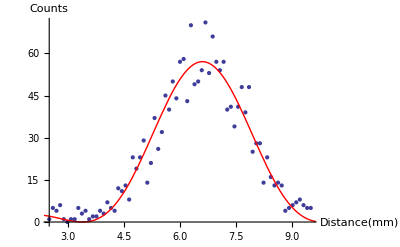

```mathematica
plotnear2=Plot[57.037926753383644 Sinc[489.0757794050044 Sin[1/500 (-6.6+x)]]^2,{x,0,10},PlotStyle->Red];
Show[ListPlot[countsnear2],plotnear2,AxesLabel-> {Distance [mm], Counts}]
```